```mathematica
ϵ=2(Cos[k1]+Kz*Cos[k2]+1);
Δ=2(Sin[k1]+Sin[k2]);
Ek=√(ϵ^2+Δ^2);
f[k1_?NumericQ,k2_?NumericQ,Kz_?NumericQ]:=(2 (1+Cos[k1]+Kz Cos[k2]))/(√(4 (1+Cos[k1]+Kz Cos[k2])^2+4 (Sin[k1]+Sin[k2])^2));
kzs = Table[kz, {kz,1,3,0.01}]; scalar =0.52/20.635243254169715;
values = scalar * NIntegrate[Evaluate@f[k1,k2,#],{k1,-3,3}, {k2,-3,3}]&/@kzs
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.52,0.518883,0.517764,0.516642,0.515519,0.514393,0.513265,0.512134,0.511002,0.509867,0.50873,0.50759,0.506448,0.505302,0.504157,0.503007,0.501856,0.500701,0.499544,0.498385,0.497223,0.496058,0.494891,0.493721,0.492548,0.491372,0.490194,0.489012,0.487828,0.48664,0.48545,0.484256,0.48306,0.48186,0.480657,0.47945,0.478241,0.477027,0.475811,0.47459,0.473366,0.472139,0.470907,0.469672,0.468433,0.46719,0.465943,0.464691,0.463436,0.462176,0.460911,0.459642,0.458369,0.45709,0.455807,0.454519,0.453226,0.451927,0.450623,0.449314,0.447999,0.446678,0.445351,0.444018,0.442679,0.441333,0.439981,0.438621,0.437255,0.435882,0.434501,0.433112,0.431715,0.43031,0.428896,0.427473,0.426041,0.4246,0.423149,0.421687,0.420214,0.41873,0.417234,0.415726,0.414205,0.41267,0.41112,0.409556,0.407975,0.406377,0.404761,0.403125,0.401467,0.399787,0.398081,0.396348,0.394583,0.392784,0.390943,0.389053,0.387101,0.385056,0.382863,0.380633,0.378405,0.376195,0.374009,0.37185,0.36972,0.367622,0.365554,0.363517,0.361512,0.359537,0.357592,0.355677,0.353792,0.351934,0.350105,0.348304,0.346528,0.34478,0.343056,0.341358,0.339683,0.338033,0.336405,0.3348,0.333217,0.331656,0.330116,0.328596,0.327096,0.325616,0.324155,0.322712,0.321288,0.319881,0.318492,0.31712,0.315765,0.314426,0.313103,0.311796,0.310503,0.309226,0.307964,0.306716,0.305482,0.304261,0.303054,0.301861,0.30068,0.299513,0.298357,0.297214,0.296083,0.294964,0.293856,0.29276,0.291675,0.2906,0.289537,0.288484,0.287442,0.286409,0.285387,0.284375,0.283372,0.282379,0.281395,0.280421,0.279455,0.278499,0.277551,0.276612,0.275681,0.274759,0.273845,0.272939,0.272041,0.271151,0.270269,0.269394,0.268527,0.267667,0.266815,0.26597,0.265132,0.2643,0.263476,0.262659,0.261848,0.261044,0.260246,0.259455,0.25867,0.257892,0.257119,0.256353,0.255592}

```mathematica
array=Transpose[{kzs, values}]
```

{{1.,0.52},{1.01,0.518883},{1.02,0.517764},{1.03,0.516642},{1.04,0.515519},{1.05,0.514393},{1.06,0.513265},{1.07,0.512134},{1.08,0.511002},{1.09,0.509867},{1.1,0.50873},{1.11,0.50759},{1.12,0.506448},{1.13,0.505302},{1.14,0.504157},{1.15,0.503007},{1.16,0.501856},{1.17,0.500701},{1.18,0.499544},{1.19,0.498385},{1.2,0.497223},{1.21,0.496058},{1.22,0.494891},{1.23,0.493721},{1.24,0.492548},{1.25,0.491372},{1.26,0.490194},{1.27,0.489012},{1.28,0.487828},{1.29,0.48664},{1.3,0.48545},{1.31,0.484256},{1.32,0.48306},{1.33,0.48186},{1.34,0.480657},{1.35,0.47945},{1.36,0.478241},{1.37,0.477027},{1.38,0.475811},{1.39,0.47459},{1.4,0.473366},{1.41,0.472139},{1.42,0.470907},{1.43,0.469672},{1.44,0.468433},{1.45,0.46719},{1.46,0.465943},{1.47,0.464691},{1.48,0.463436},{1.49,0.462176},{1.5,0.460911},{1.51,0.459642},{1.52,0.458369},{1.53,0.45709},{1.54,0.455807},{1.55,0.454519},{1.56,0.453226},{1.57,0.451927},{1.58,0.450623},{1.59,0.449314},{1.6,0.447999},{1.61,0.446678},{1.62,0.445351},{1.63,0.444018},{1.64,0.442679},{1.65,0.441333},{1.66,0.439981},{1.67,0.438621},{1.68,0.437255},{1.69,0.435882},{1.7,0.434501},{1.71,0.433112},{1.72,0.431715},{1.73,0.43031},{1.74,0.428896},{1.75,0.427473},{1.76,0.426041},{1.77,0.4246},{1.78,0.423149},{1.79,0.421687},{1.8,0.420214},{1.81,0.41873},{1.82,0.417234},{1.83,0.415726},{1.84,0.414205},{1.85,0.41267},{1.86,0.41112},{1.87,0.409556},{1.88,0.407975},{1.89,0.406377},{1.9,0.404761},{1.91,0.403125},{1.92,0.401467},{1.93,0.399787},{1.94,0.398081},{1.95,0.396348},{1.96,0.394583},{1.97,0.392784},{1.98,0.390943},{1.99,0.389053},{2.,0.387101},{2.01,0.385056},{2.02,0.382863},{2.03,0.380633},{2.04,0.378405},{2.05,0.376195},{2.06,0.374009},{2.07,0.37185},{2.08,0.36972},{2.09,0.367622},{2.1,0.365554},{2.11,0.363517},{2.12,0.361512},{2.13,0.359537},{2.14,0.357592},{2.15,0.355677},{2.16,0.353792},{2.17,0.351934},{2.18,0.350105},{2.19,0.348304},{2.2,0.346528},{2.21,0.34478},{2.22,0.343056},{2.23,0.341358},{2.24,0.339683},{2.25,0.338033},{2.26,0.336405},{2.27,0.3348},{2.28,0.333217},{2.29,0.331656},{2.3,0.330116},{2.31,0.328596},{2.32,0.327096},{2.33,0.325616},{2.34,0.324155},{2.35,0.322712},{2.36,0.321288},{2.37,0.319881},{2.38,0.318492},{2.39,0.31712},{2.4,0.315765},{2.41,0.314426},{2.42,0.313103},{2.43,0.311796},{2.44,0.310503},{2.45,0.309226},{2.46,0.307964},{2.47,0.306716},{2.48,0.305482},{2.49,0.304261},{2.5,0.303054},{2.51,0.301861},{2.52,0.30068},{2.53,0.299513},{2.54,0.298357},{2.55,0.297214},{2.56,0.296083},{2.57,0.294964},{2.58,0.293856},{2.59,0.29276},{2.6,0.291675},{2.61,0.2906},{2.62,0.289537},{2.63,0.288484},{2.64,0.287442},{2.65,0.286409},{2.66,0.285387},{2.67,0.284375},{2.68,0.283372},{2.69,0.282379},{2.7,0.281395},{2.71,0.280421},{2.72,0.279455},{2.73,0.278499},{2.74,0.277551},{2.75,0.276612},{2.76,0.275681},{2.77,0.274759},{2.78,0.273845},{2.79,0.272939},{2.8,0.272041},{2.81,0.271151},{2.82,0.270269},{2.83,0.269394},{2.84,0.268527},{2.85,0.267667},{2.86,0.266815},{2.87,0.26597},{2.88,0.265132},{2.89,0.2643},{2.9,0.263476},{2.91,0.262659},{2.92,0.261848},{2.93,0.261044},{2.94,0.260246},{2.95,0.259455},{2.96,0.25867},{2.97,0.257892},{2.98,0.257119},{2.99,0.256353},{3.,0.255592}}

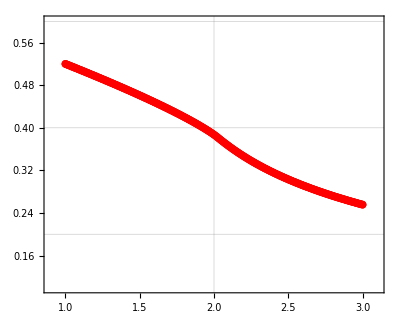

```mathematica
ListLinePlot[array,PlotRange->{{0.9,3.1},{0.1,0.6}},AspectRatio->0.8,Frame->True,FrameStyle->Thickness[0.005], PlotStyle->{Red,Thick}, Mesh->Full, GridLines->{{2,4,6,8},{0.2,0.4,0.6}},LabelStyle->{FontSize-> 18}]
```

```mathematica
Export["out.txt",array,"Table"]
```

out.txt

```mathematica
Directory[]
```

/home/shifeng